# VCO drift

P. Huft

data from Sam Norrell with VCO in a self-heterodyne module in AQuA. 2022.06.22.

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["VCO_Stability_for_Preston.xlsx"]
```

{{{Time,Frequency (MHz),,},{Tue 30 Nov -2 07:00:00GMT-5,100.116,,300 Hz bandwidth measurements},{Tue 30 Nov -2 07:05:00GMT-5,100.016,,},{Tue 30 Nov -2 07:30:00GMT-5,100.02,,},{Tue 30 Nov -2 07:45:00GMT-5,100.02,,},{Tue 30 Nov -2 08:00:00GMT-5,100.022,,},{Tue 30 Nov -2 08:30:00GMT-5,100.023,,},{Tue 30 Nov -2 09:00:00GMT-5,100.023,,},{Tue 30 Nov -2 09:15:00GMT-5,100.022,,},{Tue 30 Nov -2 09:30:00GMT-5,100.022,,},{Tue 30 Nov -2 09:50:00GMT-5,100.023,,},{Tue 30 Nov -2 10:38:00GMT-5,100.02,,},{Tue 30 Nov -2 11:08:00GMT-5,100.022,,},{Tue 30 Nov -2 11:30:00GMT-5,100.022,,}}}

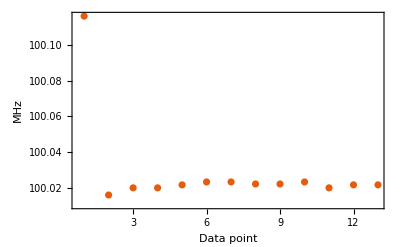

```mathematica
freq = data[[;;,2;;,2]][[1]];
ListPlot[freq,PlotTheme->"Scientific",FrameLabel->{"Data point","MHz"},PlotRange->All]
```

```mathematica
freq = freq[[3;;]];
(*Allan variance*)
Sqrt[Total[Array[(freq[[#+1]]-freq[[#]])^2&,Length[freq]-1]]/(2(Length[freq]-1))]
```

0.00104143